```mathematica
x= {0.074195,0.077316,0.144645,0.18457,0.0155,0.01528,0.016587,0.017259,.040169,0.015218,0.016171,0.017171,0.040309,0.074283,0.07781,0.094418,0.074309,0.094648}
```

{0.074195,0.077316,0.144645,0.18457,0.0155,0.01528,0.016587,0.017259,0.040169,0.015218,0.016171,0.017171,0.040309,0.074283,0.07781,0.094418,0.074309,0.094648}

```mathematica
y={.7831,.7739,.6322,.5609,.7497,.8906,.8799,.8745,.7353,.9216,.9175,.9159,.8201,.6916,.682,.6289,.753,.6975}
```

{0.7831,0.7739,0.6322,0.5609,0.7497,0.8906,0.8799,0.8745,0.7353,0.9216,0.9175,0.9159,0.8201,0.6916,0.682,0.6289,0.753,0.6975}

```mathematica
yerror={0.055598068831649056,0.05565946112367823,0.05988844097161335,0.06468771208062003,0.056778153289081264,0.056790741874237036,0.05671681442058604,0.05667961088802918,0.05574608076965043,0.056794300137805814,0.05674011993663505,0.056684451550889484,0.05574241080774617,0.05559962807812941,0.05567032633503662,0.05621644771550726,0.055600090674116386,0.05622645161876277}
```

{0.0555981,0.0556595,0.0598884,0.0646877,0.0567782,0.0567907,0.0567168,0.0566796,0.0557461,0.0567943,0.0567401,0.0566845,0.0557424,0.0555996,0.0556703,0.0562164,0.0556001,0.0562265}

```mathematica
plotyvalues=Table[Around[y[[i]],yerror[[i]]],{i,1,Length[y]}]
```

{0.780.06,0.770.06,0.630.06,0.560.06,0.750.06,0.890.06,0.880.06,0.870.06,0.740.06,0.920.06,0.920.06,0.920.06,0.820.06,0.690.06,0.680.06,0.630.06,0.750.06,0.700.06}

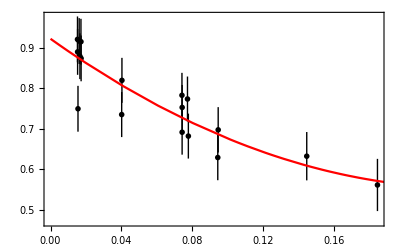

```mathematica
Show[ListPlot[Transpose[{x,plotyvalues}],PlotTheme->"Monochrome"], Plot[0.9230341547832125-3.1306483061897628 c+6.624164579175652 c^2,{c,0,1},PlotStyle->{Red}],Frame->True]
```

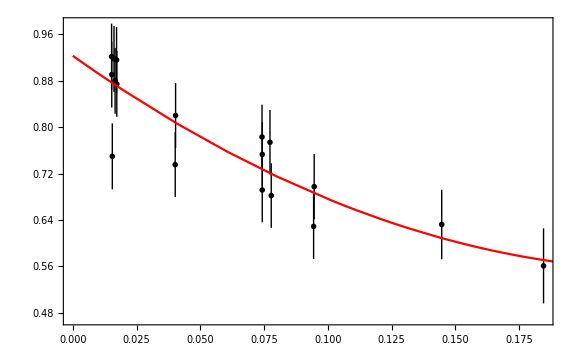

```mathematica
Show[%5,ImageSize->Large]
```

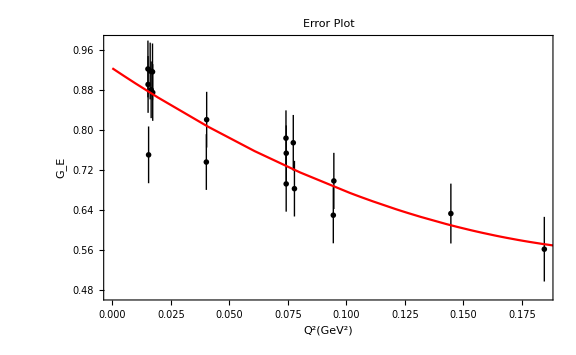

```mathematica
Show[%6,FrameLabel->{{HoldForm[Subscript[G, "E"]],None},{HoldForm[(Q^2)[GeV^2]],None}},PlotLabel->HoldForm[Error Plot],LabelStyle->{14,GrayLevel[0],Bold}]
```

```mathematica
Show[%7,FrameLabel->{{HoldForm[Subscript[G, "E"]],None},{HoldForm[Q^2(GeV^2)],None}},PlotLabel->HoldForm[Error Plot],LabelStyle->{14,GrayLevel[0],Bold}]
```

Show::gtype: Out is not a type of graphics.

Show[%7,FrameLabel→{{G_E,None},{Q^2 GeV^2,None}},PlotLabel→Error Plot,LabelStyle→{14,GrayLevel[0],Bold}]

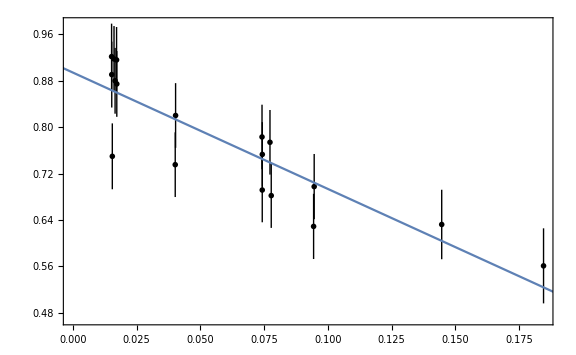

```mathematica
Show[%5,ImageSize->Large]
```

```mathematica
Show[%6,FrameLabel->{{HoldForm[Subscript["G", "E"]],None},{HoldForm[Q^2],None}},PlotLabel->HoldForm[Error Plot],LabelStyle->{12,GrayLevel[0],Bold}]
```

Show::gtype: Out is not a type of graphics.

Show[%6,FrameLabel→{{G_E,None},{Q^2,None}},PlotLabel→Error Plot,LabelStyle→{12,GrayLevel[0],Bold}]

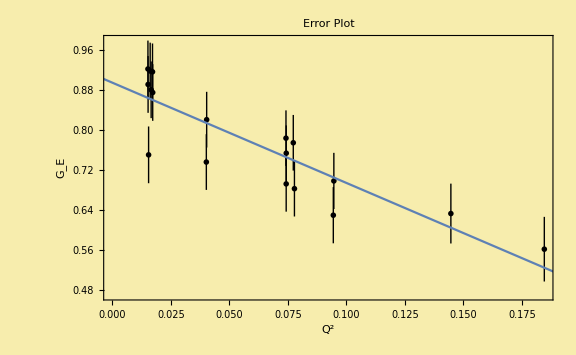

```mathematica
Show[%7,Background->RGBColor[0.97,0.93,0.68]]
```

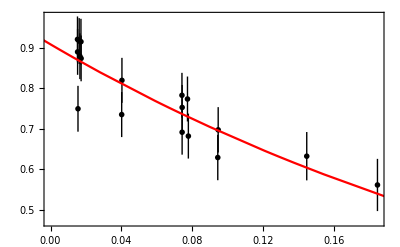

```mathematica
Show[ListPlot[Transpose[{x,plotyvalues}],PlotTheme->"Monochrome"], Plot[0.9092689759118766 ⅇ^(-2.8332598305453485 t),{t,-6.353105989765629,6.353105989765629},PlotStyle->{Red}],Frame->True]
```

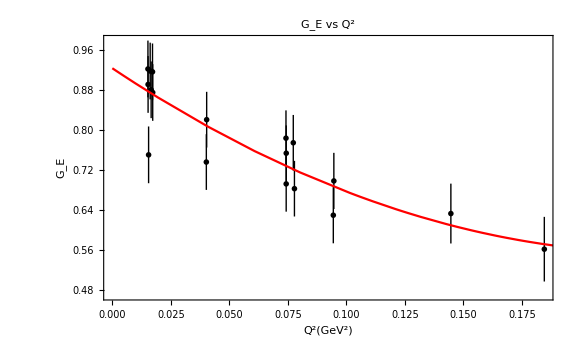

```mathematica
Show[%6,FrameLabel->{{HoldForm[Subscript[G, "E"]],None},{HoldForm[(Q^2)[GeV^2]],None}},PlotLabel->HoldForm[Subscript[G, "E"] vs Q^2],LabelStyle->{14,GrayLevel[0],Bold}]
```